```mathematica
s=2*Exp[37166.4*t]+2*Exp[-37166.4*t]+0;
ds=-D[Log[s], t]/12;
t:=1/T;
dss=D[ds, T];
```

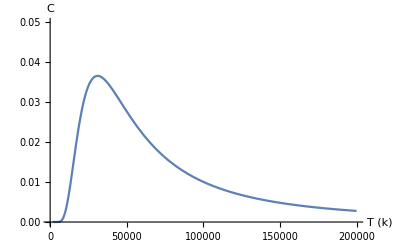

```mathematica
Plot[dss,{T,0.001,200000}, PlotRange->{0,0.05}, AxesLabel->{"T (k)","C"}]
```